\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Introduction to Mathematica (MMA) -- 01

Zu-Cheng Chen

Institute of Theoretical Physics, 
Chinese Academy of Sciences

@ Guangzhou University, Jul 2019

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Overview of Mathematica (MMA)

## Easy to learn/use

Many predefined functions.
Press Shift+Enter to evaluate cells.

```mathematica
Print["Hello, World!"]
```

Hello, World!

## Dynamical language

Define a function.

```mathematica
f[x_]:=x^2
f[2]
```

4

No need to declare types of variables.
Redefine variable dynamically.

```mathematica
f[x_]:=x^3
f[2]
```

8

```mathematica
f = 3
```

3

## Symbolic calculation

```mathematica
Integrate[x*Sin[x^2],x]
```

-1/2 Cos[x^2]

```mathematica
Integrate[x*Sin[x^2],{x,-1,3}]
```

1/2 (Cos[1]-Cos[9])

## Visualization

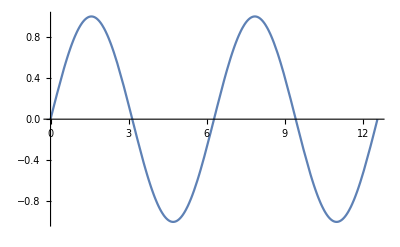

```mathematica
Plot[Sin[x],{x,0,4*π}]
```

## Relatively slow to run, but fast to write.

Suppose 

 C : 1000 lines; 1 day to write; 1 minute to run; 
MMA : 50 lines; 1 hour to write; 1 hour to run; 

Will you choose C or MMA ?

## Property software: not open, neither free

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Be familiar with notebook

## Cells

Input cell;
Output cell;
Cell groups;

```mathematica
Print["Hello, World!"]
```

Hello, World!

## Styles: Format->Style

Alt+1: Title
Alt+2: Subtitle
...
Alt+6: Subsubsection
...

## Help system: F1 ? ??

```mathematica
Integrate[BesselJ[n,x],x]
```

2^(-1-n) x^(1+n) Gamma[(1+n)/2] HypergeometricPFQRegularized[{(1+n)/2},{1+n,(3+n)/2},-x^2/4]

```mathematica
?BesselJ
```

```mathematica
??BesselJ
```

## Comments: Alt+/

```mathematica
(*This is a comment*)
```

```mathematica
(*f[x] gives the square of x.*)
f[x_]:=x^2
```

## Suppress outputs ( ; )

```mathematica
1+1
```

2

```mathematica
1+1;
```

## Last output: %

```mathematica
1+1
%
```

2

2

## Timing

```mathematica
Clear[x];
Integrate[Sin[x],x]//Timing
```

{0.002094,-Cos[x]}

```mathematica
Integrate[Sin[x],x]//Timing
Integrate[Sin[x],x]//AbsoluteTiming
```

{0.00202,-Cos[x]}

{0.00155,-Cos[x]}

## Abort an evaluation: Alt+. Evaluation->Quit Kernel->Local

```mathematica
f[x_]:=(Sin[x]/x^4-Cos[x]/x^3)^100;
Integrate[f[x],x];//Timing
```

$Aborted

## Fullscreen: F12

## Better format

```mathematica
(*Esc+pi+Esc*)
Pi==π
```

True

```mathematica
(*x;ctrl+^;2*)
x^2==x^2
```

True

```mathematica
(*ctrl+2;3*)
Sqrt[3]==√3
```

True

## Clear/Remove variables

```mathematica
?f
```

### Clear

```mathematica
Clear[f]
?f
```

```mathematica
a=3
?a
```

3

### Unset (.)

```mathematica
a=.
?a
```

### Remove

```mathematica
a=3
Remove[a]
?a
```

3

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Function -- part 1

## Define a function: f[x_]:=a*x+b

```mathematica
a=3;
b=2;
```

### Correct way

```mathematica
Clear[f]
f[x_]:=a*x+b
?f
```

```mathematica
f[3]
```

11

### Wrong way 1: f[x]:=a*x+b

```mathematica
Clear[f]
f[x]:=a*x+b
?f
```

```mathematica
f[3]
```

f[3]

```mathematica
f[x]
```

2+3 x

### Wrong way 2: f[x_]=a*x+b

```mathematica
x=5;
```

```mathematica
Clear[f]
f[x_]=a*x+b
?f
```

17

```mathematica
f[3]
```

17

```mathematica
f[x]
```

17

```mathematica
f[4]
```

17

### Wrong way 3: f[x]=a*x+b

```mathematica
x=5;
```

```mathematica
Clear[f]
f[x]=a*x+b
?f
```

17

```mathematica
f[3]
```

f[3]

```mathematica
f[x]
```

17

```mathematica
f[4]
```

f[4]

## Set(=) and SetDelayed(:=)

```mathematica
x=1;
a = x+1;
b:=x+1;
```

```mathematica
{a,b}
```

{2,2}

```mathematica
x=2;
{a,b}
```

{2,3}

```mathematica
?a
```

```mathematica
?b
```

### Exercise

```mathematica
c = RandomReal[ ]; 
d := RandomReal [ ];
```

Will following expressions all equals to 0?
Can you explain why?
c - c
c - d
d - d

## Pattern

```mathematica
Clear[g,f,x]
g[x]=x+1; 
f[x_]=x+1;
```

```mathematica
{g[x],f[x]}
```

{1+x,1+x}

```mathematica
{g[y],f[y]}
```

{g[y],1+y}

```mathematica
x=2;
{g[x],f[x]}
```

{g[2],3}

### Exercise

What is the result of f[3] if function f is defined as:
x = 2; 
f[x_] = x + 1;

## Call a function: f[x_]:=x^2 f[2] f@2 2//f

```mathematica
f[x_]:=x^2
```

```mathematica
f[2]
```

4

```mathematica
f@2
```

4

```mathematica
2//f
```

4

```mathematica
f[x_,y_]:=x+y
```

```mathematica
2~f~3
```

5

## Piecewise function

```mathematica
Clear@f;
f[x_]:=Piecewise[{
{x^2,x<0},
{x,x>0}
}]
```

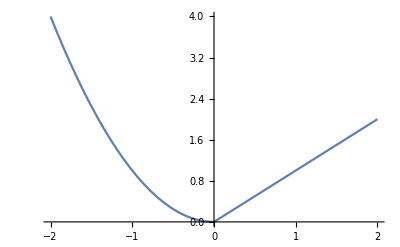

```mathematica
Plot[f[x],{x,-2,2}]
```

## An example: Fibonacci Sequence

1, 1, 2, 3, 5, 8, 13, 21, 34, ...
F_n = F_(n-1) + F_(n-2)

Question: what is F_20 and F_40?

### Original version

```mathematica
Clear@fib;
fib[1]=1;
fib[2]=1;
fib[n_]:=fib[n-1]+fib[n-2]
```

```mathematica
fib[30]//AbsoluteTiming
```

{1.14305,832040}

### Improved version